## π^+π^+—>π^+π^+

```mathematica
setphysics={u->4*0.13957^2-t-s,Subscript[F, 0]->0.092,Subscript[g, v]->0.17,Subscript[m, π]->0.13957,Subscript[m, ρ]->0.77526};
```

#### Scattering amplitude using Mandelstam variables

```mathematica
ℳ= Subscript[g, v]^2/(4*Subscript[F, 0]^4)((t^2*(s-u))/(t-Subscript[m, ρ]^2)+(u^2*(s-t))/(u-Subscript[m, ρ]^2));
```

#### The differential cross section: dσ/dt=1/(64πs)1/(|p_(1_CM)|^2)(|ℳ|)^2

p_(1_CM)=√(s/4-m_π^2)=p_(3_CM) since the masses are the same. Generally p_i_CM= √(E_i^2-m_i^2) where E_(1/2)=(s+(m_(1/2))^2-(m_(2/1))^2)/(2 √s) and E_(3/4)=(s+(m_(3/4))^2-(m_(4/3))^2)/(2 √s)

```mathematica
Subscript[p, Subscript[1, CM]]=Sqrt[s/4-Subscript[m, π]^2]/.setphysics;
```

```mathematica
crosssection[s_]:=Evaluate[1/(64π s)1/Subscript[p, Subscript[1, CM]]^2 Abs[ ℳ]^2/.setphysics];
```

#### Integration limit

t_1=((m_1^2-m_2^2-m_3^2+m_4^2)/(2 √s))^2-(p_(1_cm)+p_(3_CM))^2
t_0=((m_1^2-m_2^2-m_3^2+m_4^2)/(2 √s))^2-(p_(1_cm)-p_(3_CM))^2

```mathematica
Subscript[t, 1][s_]:=Evaluate[-(2*Subscript[p, Subscript[1, CM]])^2/.setphysics]
Subscript[t, 0]=0;
```

#### Integrate the cross section

```mathematica
sigma[s_?NumericQ]:=NIntegrate[crosssection[s],{t,Subscript[t, 1][s],Subscript[t, 0]}]
```

#### Energy limit

s_min=4 m_π^2
s_max=10^6 MeV^2=1 GeV^2

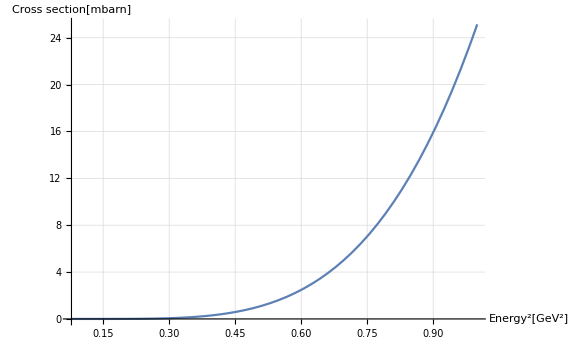

```mathematica
Plot[0.389*sigma[s],{s,4*Subscript[m, π]^2/.setphysics,1}, Axes->True,AxesLabel->{Style["Energy^2[GeV^2]",Bold,16],Style["Cross section[mbarn]",Bold,16]},GridLines->Automatic,ImageSize->Large]
```

## π^+π^-—>π^+π^-

```mathematica
setphysics={u->4*0.13957^2-t-s,Subscript[F, 0]->0.092,Subscript[g, v]->0.17,Subscript[m, π]->0.13957,Subscript[m, ρ]->0.77526,Γ->0.1474};
```

#### Scattering amplitude using Mandelstam variables

```mathematica
ℳ= Subscript[g, v]^2/(4*Subscript[F, 0]^4)((s^2*(u-t))/(s-Subscript[m, ρ]^2)+(t^2*(u-s))/(t-Subscript[m, ρ]^2));
Subscript[ℳ, damp]= Subscript[g, v]^2/(4*Subscript[F, 0]^4)((s^2*(u-t))/(s-Subscript[m, ρ]^2+I*Subscript[m, ρ]*Γ)+(t^2*(u-s))/(t-Subscript[m, ρ]^2));
```

#### The differential cross section: dσ/dt=1/(64πs)1/(|p_(1_CM)|^2)(|ℳ|)^2

p_(1_CM)=√(s/4-m_π^2)=p_(3_CM) since the masses are the same. Generally p_i_CM= √(E_i^2-m_i^2) where E_(1/2)=(s+(m_(1/2))^2-(m_(2/1))^2)/(2 √s) and E_(3/4)=(s+(m_(3/4))^2-(m_(4/3))^2)/(2 √s)

```mathematica
Subscript[p, Subscript[1, CM]]=Sqrt[s/4-Subscript[m, π]^2]/.setphysics;
```

```mathematica
crosssection[s_]:=Evaluate[1/(64π s)1/Subscript[p, Subscript[1, CM]]^2 Abs[ℳ]^2/.setphysics];
crosssectiondamp[s_]:=Evaluate[1/(64π s)1/Subscript[p, Subscript[1, CM]]^2 Abs[Subscript[ℳ, damp]]^2/.setphysics];
```

#### Integration limit

t_1=((m_1^2-m_2^2-m_3^2+m_4^2)/(2 √s))^2-(p_(1_cm)+p_(3_CM))^2
t_0=((m_1^2-m_2^2-m_3^2+m_4^2)/(2 √s))^2-(p_(1_cm)-p_(3_CM))^2

```mathematica
Subscript[t, 1][s_]:=Evaluate[-(2*Subscript[p, Subscript[1, CM]])^2/.setphysics]
Subscript[t, 0]=0;
```

#### Integrate the cross section

```mathematica
sigma[s_?NumericQ]:=NIntegrate[crosssection[s],{t,Subscript[t, 1][s],Subscript[t, 0]}]
sigmadamp[s_?NumericQ]:=NIntegrate[crosssectiondamp[s],{t,Subscript[t, 1][s],Subscript[t, 0]}]
```

#### Energy limit

s_min=4 m_π^2
s_max=10^6 MeV^2=1 GeV^2

#### Plot resonance with and without damping

```mathematica
plot=Show[Plot[0.389*sigma[s],{s,4*Subscript[m, π]^2/.setphysics,1}, Axes->True,AxesLabel->{Style["Energy^2[GeV^2]",Bold,16],Style["Cross section[mbarn]",Bold,16]},GridLines->Automatic,PlotLegends->Placed[{"without dumpling"},{1,0.5}]],
Plot[0.389*sigmadamp[s],{s,4*Subscript[m, π]^2/.setphysics,1}, Axes->True,AxesLabel->{Style["Energy^2[GeV^2]",Bold,16],Style["Cross section[mbarn]",Bold,16]},GridLines->Automatic,PlotStyle->Red,PlotLegends->Placed[{"with dumpling"},{1,0.5}]],ImageSize->Large]
Export["/media/fb/Data150/Iroda/uppsala/QCD/pipluspiminusdumpling.png",plot]
```

-Graphics-

/media/fb/Data150/Iroda/uppsala/QCD/pipluspiminusdumpling.png

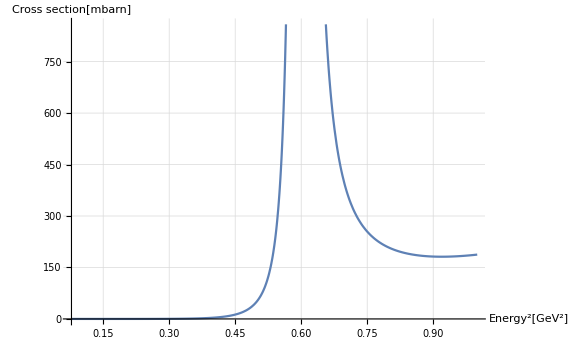

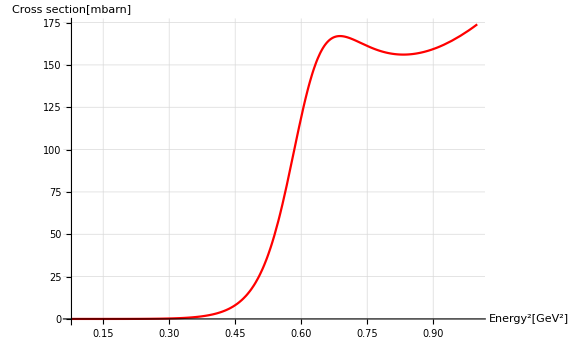

```mathematica
Plot[0.389*sigma[s],{s,4*Subscript[m, π]^2/.setphysics,1}, Axes->True,AxesLabel->{Style["Energy^2[GeV^2]",Bold,16],Style["Cross section[mbarn]",Bold,16]},GridLines->Automatic, ImageSize->Large]

Plot[0.389*sigmadamp[s],{s,4*Subscript[m, π]^2/.setphysics,1}, Axes->True,AxesLabel->{Style["Energy^2[GeV^2]",Bold,16],Style["Cross section[mbarn]",Bold,16]},GridLines->Automatic,PlotStyle->Red,ImageSize->Large]
```

```mathematica
Show[Plot[0.389*sigma[s],{s,4*Subscript[m, π]^2/.setphysics,0.56}, PlotRange->{{4*Subscript[m, π]^2/.setphysics,0.5},Automatic},Axes->True,AxesLabel->{Style["Energy^2[GeV^2]",Bold,16],Style["Cross section[mbarn]",Bold,16]},GridLines->Automatic,ImageSize->Large,PlotLegends->Placed[{"without damping"},{1,0.5}]],Plot[0.389*sigmadamp[s],{s,4*Subscript[m, π]^2/.setphysics,0.55},PlotRange->{{4*Subscript[m, π]^2/.setphysics,0.5},Automatic}, Axes->True,AxesLabel->{Style["Energy^2[GeV^2]",Bold,16],Style["Cross section[mbarn]",Bold,16]},GridLines->Automatic,ImageSize->Large,PlotLegends->Placed[{"with damping"},{1,0.5}],PlotStyle->Red]]
```

-Graphics-